# Sensitivity Analysis for blinking light

I analyzed the frequency of the circuit and its sensitivity to manufacturing tolerance using LTspice.
In the diagram below, mc(x,μ) represents an unknown value in the range [x(1-μ) ... x(+μ)], so mc(110k, 0.01) is the tolerance band on a 1% 110kΩ resistor.

-Graphics-

## Analysis

```mathematica
SetDirectory@NotebookDirectory[];
{n,cap,freq,pd}=Transpose[Import["LTspice/freq_data.txt","Data"][[2;;All]]];
Length[freq]
```

500

```mathematica
MinMax[freq]
```

{0.901583,1.1204}

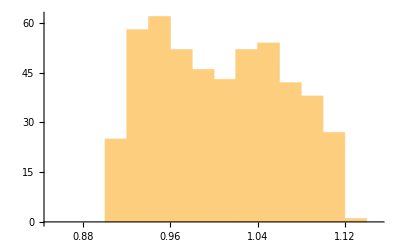

```mathematica
Histogram[freq,PlotRange->{{0.85,1.15},Automatic}]
```

As required, the frequency always falls within 1hz ± 15%.

Additional analysis reveals that the variability in frequency is almost entirely determined by the capacitor.

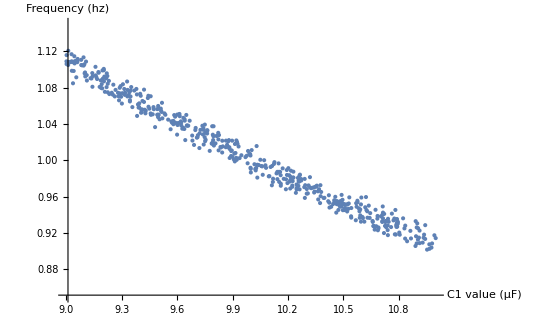

```mathematica
ListPlot[Transpose@{cap*10^6, freq},
AxesLabel->{"C1 value (μF)", "Frequency (hz)"},
PlotRange->{{9,11},{.85,1.15}}]
```